```mathematica
Clear["Global`*"];
Needs["INVARIANT`"];
$HistoryLength=0;
```

## Coefficients

### TraningSets

```mathematica
volume=1687.51;
TrainingPhases0={
{"p3",-152.1,{0.,0.,0.,0.,0.,0.,0.,0.,-0.8891490107962782,0.,0.,0.,0.,0.,0.}},{"-p3",-182.4,{0.,0.,0.,0.,0.,0.,0.,0.,-0.9015558876187322,0.0005513122036847985,0.0005387120433698457,0.0007150092401915159,-0.0017757910935031953,0.,0.}},
{"-p1-p2-p3",-282.5,{0.,0.,0.,0.,0.,0.,-0.7176344120790196,-0.7176344120790196,-0.7176344120790196,0.,0.,0.,0.,0.,0.}},
{"p1p2p3",-192.8,{0.,0.,0.,0.,0.,0.,0.608258813088639,0.608258813088639,0.608258813088639,0.,0.,0.,0.,0.,0.}},
{"-p1-p2-p3",-326.1,{0.,0.,0.,0.,0.,0.,-0.7350970564490107,-0.7350970564490107,-0.7350970564490107,0.0011612913717867952,0.001161176230378216,0.0011610609717952265,-0.00016983054690444425,-0.00016994574688701555,-0.00016988814689573018}},
{"c1",-70.9,{0.,0.,0.,0.,0.,0.8272506285280175,0.,0.,0.,0.,0.,0.,0.,0.,0.}},
{"c1c2",-112.8,{0.,0.,0.,0.,0.6990514021157528,0.6990514021157528,0.,0.,0.,0.,0.,0.,0.,0.,0.}},
{"b2c2",-147.2,{0.,0.,0.,0.7089241979929871,0.6606532137210868,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},
{"b1c2",-89.3,{0.,0.,0.49656551793293097,0.,-0.49656551793293097,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},
{"-a2b2c2",-397.3,{0.,-1.003550323750633,0.,1.0036578657092268,1.003569214952312,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}},
{"c1c2e",-145.4,{0.,0.,0.,0.,0.7137941182161702,0.7137941182161702,0.,0.,0.,0.00045629161121641076,0.00045044341978066815,0.0013475045156530101,0.0012096962422901637,0.,0.}},
{"c1c2-p3",-645.6,{0.,0.,0.,0.,1.2121676802736494,1.2121676802736494,0.,0.,-1.4517927527026715,0.,0.,0.,0.,0.,0.}},
{"c1c2",-220.7,{0.,0.,0.,0.,0.6847003185335903,0.6847003185335903,0.,0.,0.6463383213921329,0.,0.,0.,0.,0.,0.}},
{"c1c2-p3",-794.2,{0.,0.,0.,0.,1.2677057804553862,1.2677057804553862,0.,0.,-1.5289290820047867,0.0042896492702477595,0.004263440640606502,0.0037936956438312454,0.0025706082701694513,0.,0.}}};
TrainingPhases1={
{"-e",-9.4,{0,0,0,0,0,0,0,0,0,0,0,0,-0.1699 10^-3,-0.1699 10^-3,-0.1699 10^-3}},
{"e",-6.9,{0,0,0,0,0,0,0,0,0,0,0,0,0.1699 10^-3,0.1699 10^-3,0.1699 10^-3}},
{"-c1c2e",-126.0,{0.,0.,0.,0.,0.7137941182161702,-0.7137941182161702,0.,0.,0.,0.00045629161121641076,0.00045044341978066815,0.0013475045156530101,0.0012096962422901637,0.,0.}},
{"a2-b2-c2",-230.0,{0,0.7272,0,-0.7272,-0.7272,0,0,0,0,0,0,0,0,0,0}},
{"pe",123.8,{0.,0.,0.,0.,0.,0.,0.,0.,0.9015558876187322,0.0005513122036847985,0.0005387120433698457,0.0007150092401915159,-0.0017757910935031953,0.,0.}}};
TSdir="/home/paulchern/Documents/Workshop/Working/Boracites/ISOTROPY/PBEsolU/TrainingSets/";
DFTfile={"X5.dat","P.dat","PX5.dat","eta.dat","Q1111-pe.dat","Q1122-pe.dat","Q1212-pppe.dat","gammaxc-c1c2e.dat","gammac-cubic.dat"};
{tsX5,tsP,tsPX5,tseta,tsQ1111,tsQ1122,tsQ1212,tsgammaxc,tsgammac}={#[[1]],#[[2]],#[[3;;]]}&/@Import[TSdir<>#,"Table"]&/@DFTfile;
ElasticModuli=GetElasticModuli["/home/paulchern/QMT/Boracites/DFT/Cu3B7O13Cl/VASP/GGAU/F-43c/hessian/ElasticModuli.dat",volume]
```

{C_1111→2630.72,C_1122→787.953,C_1212→1039.29}

### Fitting

```mathematica
BoraModel=LandauInvariant["OnSite"]/.{XX_[x,y,z]->XX};
TrainingSet={Join[tsP,tsQ1111,tsQ1122,tsQ1212,TrainingPhases0[[1;;5]]],Join[tsX5,tsgammaxc,TrainingPhases0[[6;;11]]],Join[tsPX5,tseta,TrainingPhases0[[12;;14]]]};
TempCoeff=ElasticModuli;
Do[gf=GoalFunction[BoraModel,volume,ts,TempCoeff];
TempCoeff=Join[TempCoeff,FitTrainingSet[gf]];
,{ts,TrainingSet}]
Print[TempCoeff];
```

Fitting error is 0.00403136

Fitting error is 0.0022086

Fitting error is 0.000744084

{C_1111→2630.72,C_1122→787.953,C_1212→1039.29,β_11→-0.504477,β_1111→0.174591,β_1122→0.167076,γ_p→0.113603,Q_1111→0.00156177,Q_1122→0.00209644,Q_1212→0.00457593,γ_pc→-6.82245,α_xx→-0.141613,α_xxxx→0.117507,α_xxXX→-0.192626,α_xxyy→-0.26145,α_xxYY→-0.183314,γ_x5→-0.0826588,γ_xc→-5.76589,η_a1b2p3→7.45305,η_c1c2p3→-0.080697,η_a2b1p3→7.40847,γ_xp→0.149026}

## Simulation

### setup mesh and parameters

{Δ1→2,Δ2→2,Δ3→2,Gx_1111→1.,Gx_1122→0,Gx_1212→1.,Gp_1111→1,Gp_1122→0,Gp_1212→1,C_1111→2630.72,C_1122→787.953,C_1212→1039.29,β_11→-0.504477,β_1111→0.174591,β_1122→0.167076,γ_p→0.113603,Q_1111→0.00156177,Q_1122→0.00209644,Q_1212→0.00457593,γ_pc→-6.82245,α_xx→-0.141613,α_xxxx→0.117507,α_xxXX→-0.192626,α_xxyy→-0.26145,α_xxYY→-0.183314,γ_x5→-0.0826588,γ_xc→-5.76589,η_a1b2p3→7.45305,η_c1c2p3→-0.080697,η_a2b1p3→7.40847,γ_xp→0.149026}

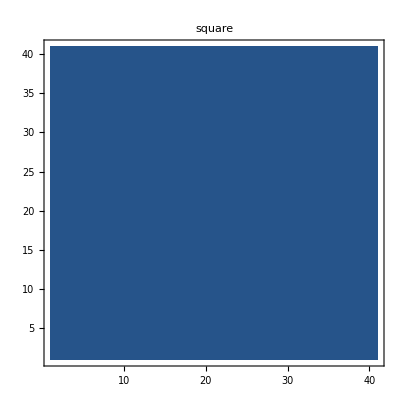
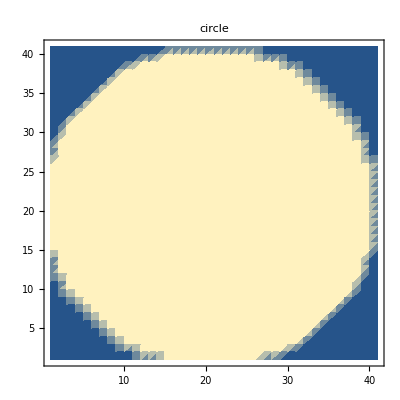
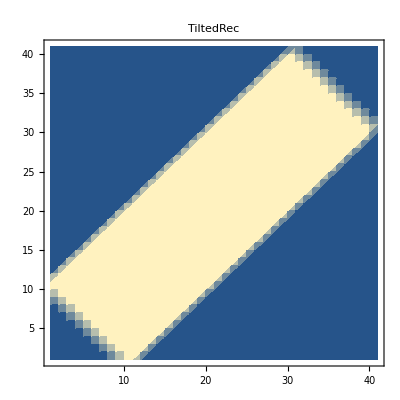
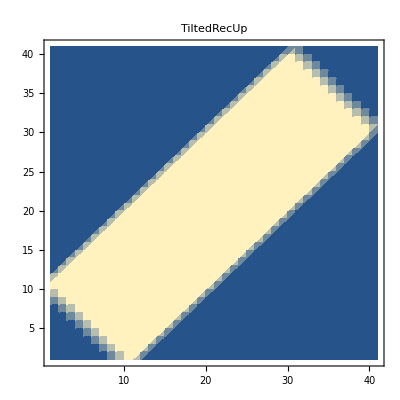
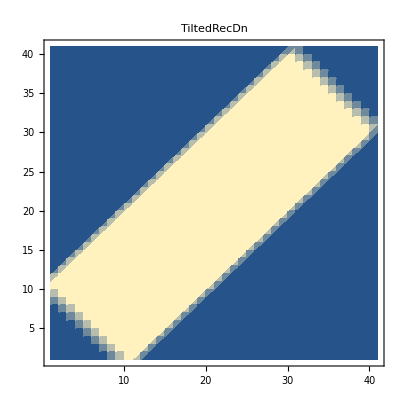
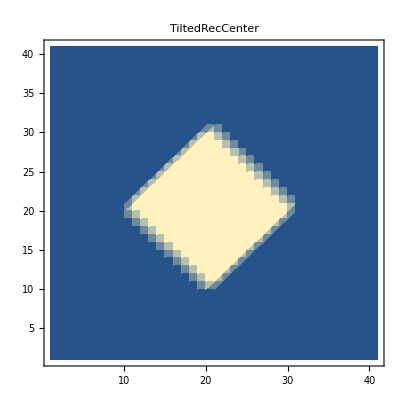
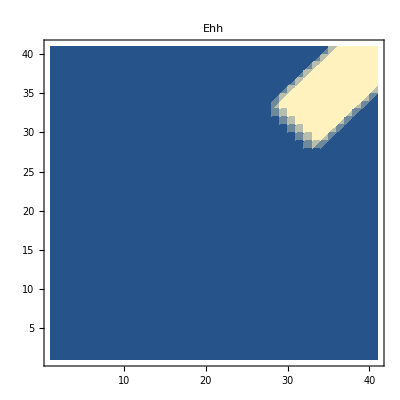
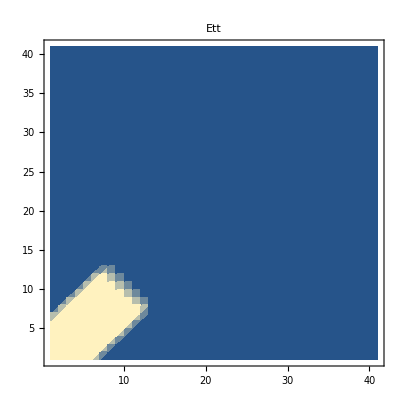

```mathematica
param=Join[{Δ1->2,Δ2->2,Δ3->2 ,Subscript[Gx, 1111]->1.0,Subscript[Gx, 1122]->0,Subscript[Gx, 1212]->1.0,Subscript[Gp, 1111]->1,Subscript[Gp, 1122]->0,Subscript[Gp, 1212]->1},TempCoeff]
Lx=41;Ly=41;Lz=2;
MaskList=ListDensityPlot[Table[MeshMask[#,{Lx,Ly,Lz},x,y,1],{x,1,Lx},{y,1,Ly}]ᵀ,AspectRatio->Lx/Ly,PlotLabel->#]&/@{"square","circle","TiltedRec","TiltedRecUp","TiltedRecDn","TiltedRecCenter","Ehh","Ett","Enarrow1","Enarrow2","EnarrowVertical"}
```

### discretization

```mathematica
zbc=Dispatch[{Subscript[u, 3,x_,y_,Lz+1]:>Subscript[u, 3,x,y,1]}];
xbc=Dispatch[{Subscript[u, 3,Lx+1,y_,z_]:>Subscript[u, 3,1,y,z]}];
```

```mathematica
meshtype="square";
fDisc0=LandauInvariant["Discretized"];
fDisc = Sum[MeshMask[meshtype,{Lx,Ly,Lz},x,y,z]fDisc0, {x, Lx}, {y, Ly}, {z, Lz}]/.param//Expand;
Length[vars=Variables@fDisc]
```

62484

## Minimization

```mathematica
NT=10;
Efields=Table[-{Sin[(2 Pi)/NT Δt],Sin[(2 Pi)/NT Δt],Sin[(2 Pi)/NT Δt]}*{1,1,1},{Δt,0,10}];
```

```mathematica
{pdata,min}=MinimizeBoracite["6",{Lx,Ly,Lz},fDisc,100000,"Ehh",Efields,10000,"TimeSeries"->True];
```

Minimizing without electric field.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Initializing minimization took 3200.51 seconds.

Applying electric field

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

Electric time step took 35.0934 seconds.

Electric time step took 1261.47 seconds.

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

Electric time step took 603.746 seconds.

Electric time step took 35.9219 seconds.

Electric time step took 625.793 seconds.

Electric time step took 1002.8 seconds.

Electric time step took 1127.15 seconds.

Electric time step took 821.52 seconds.

Electric time step took 36.104 seconds.

Electric time step took 656.755 seconds.

Electric time step took 1646.06 seconds.

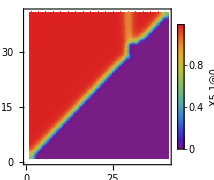
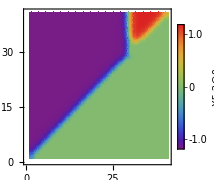
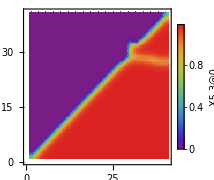
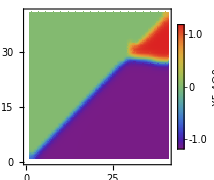
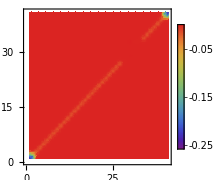
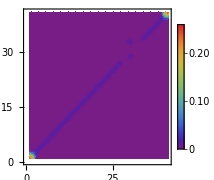
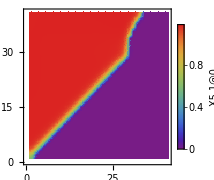
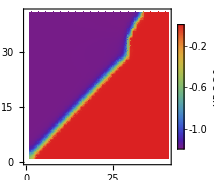
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
CompareOP[pdata,min,{1,6},{Lx,Ly,Lz},"separated"]
```

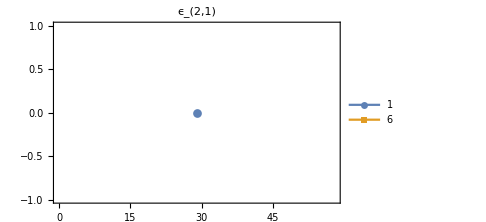
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics-

```mathematica
PathPlot[min,{1,6},19,2,param]
```